Genez, Inc.
9617 Black Watch Court
Charlotte, NC 28277

March 8, 2021

To: Chief Scientist, Vertextin Inc.
From: Aakriti Lakshmanan
Subj: QSAR Study of FKBP Drugs

## Summary and Introduction

### Abstract:

As requested in the Scope of Work of March 5, 2021, we evaluated a dataset of 6 compounds that contains the energy, dipole, HOMO, LUMO, HOMOLUMO Gap, ElPotMin, ElPotMax and Ki values for each of the compounds in order to find a representative QSAR model for predicting Ki.

### Introduction/Background Information:

FKBPs, otherwise known as FK506-binding proteins, are part of the immunophilin family. Immunophilins are isomerases that work specifically on peptide chains containing the amino acid proline. Specifically, they will act as a catalyst for the conversion between the cis and trans isomers of such peptide bonds. This activity is otherwise known cis-trans peptidyl-prolyl isomerase activity. Immunophilins are commonly seen as receptor targets for immunosuppressive drugs. [1] FKBPs are very important protein receptors, as they play a role in many different processes, including protein folding, protein trafficking, transcription and receptor signaling. [2] They also play a role in T-cell activation, which is why they are often a target receptor for immunosuppressive drugs. This family of proteins can be found in all eukaryotes and almost all tissues. [3] However, they appear in higher concentrations in nervous tissues than in immune tissues, which may mean that they also have biological activity with neurons. [2] Because of this connection, drugs that interact with FKBPs may also be potential treatments for neurodegenerative diseases. A list of current drugs that target these receptors are:

FK506 (tacrolimus)

rapamycin (sirolimus)

cyclosporin A (CsA)

analogs of these drugs

## Methodology

For this study, the list of 22 substitutions of the lead drug was collected from the NCSSM Canvas website. The following analyses were conducted:

Drug data was imported into Mathematica

Data was summarized through descriptive statistics

A multiple regression analysis was performed

The optimal Hammett Constant value was calculated

### Data Import and Description:

```mathematica
sixDrug = Import["/Users/aakritilakshmanan/Downloads/sixdrugqsar.csv"];
viableDrug=sixDrug;
sixDrug // TableForm
```

Cmpd | Energy | Dipole | HOMO | LUMO | HOMOLUMO Gap | ElPotMin | ElPotMax | Ki
1 | -89.8594 | 5.035 | -0.21657 | 0.0082 | 0.22477 | -2.82719 | -1.13415 | 7.2
2 | -71.1931 | 4.548 | -0.22868 | -0.00362 | 0.22506 | -2.68957 | -1.08135 | 6.5
3 | -118.553 | 4.683 | -0.21866 | 0.00832 | 0.22698 | -3.23607 | -1.03287 | 0.79
4 | -159.645 | 4.206 | -0.2234 | 0.00521 | 0.22861 | -3.01286 | -1.01623 | 8.4
5 | -119.092 | 3.963 | -0.22772 | 0.00753 | 0.23525 | -3.05296 | -0.9378 | 0.57
6 | -123.927 | 4.585 | -0.22783 | 0.00979 | 0.23762 | -3.23386 | -1.00829 | 0.55

## Results

### Descriptive Statistics

We determined the mean, median, standard deviation, and quartiles for specific parameters within our data set, and produced a box/whisker plot for each of the variables.

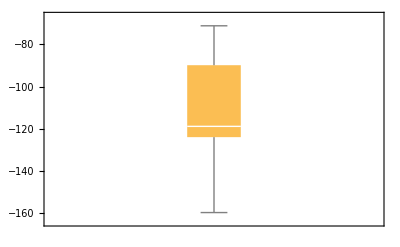
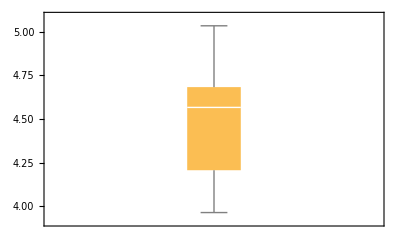
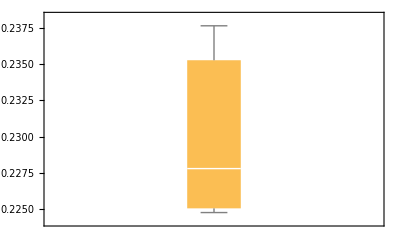
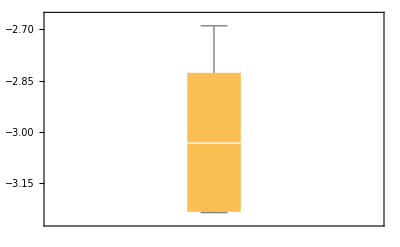
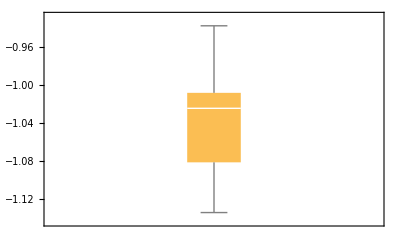
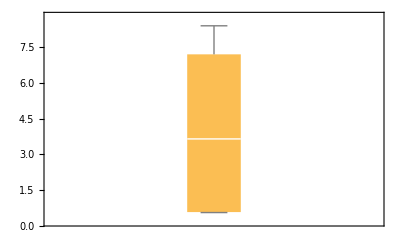
| Energy | Dipole | HOMOLUMO Gap | ElPotMin | ElPotMax | Ki
Mean | -113.712 | 4.50333 | 0.229715 | -3.00875 | -1.03512 | 4.00167
Median | -118.822 | 4.5665 | 0.227795 | -3.03291 | -1.02455 | 3.645
Standard Deviation | 30.4742 | 0.375228 | 0.00543964 | 0.218705 | 0.0670777 | 3.73688
Quartiles | {-123.927,-118.822,-89.8594} | {4.206,4.5665,4.683} | {0.22506,0.227795,0.23525} | {-3.23386,-3.03291,-2.82719} | {-1.08135,-1.02455,-1.00829} | {0.57,3.645,7.2}
BoxWhisker Plot | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
header = sixDrug[[1]];
sixDrug = Delete[sixDrug,1];
{cmpd,energy,dipole,homo,lumo,holo,elpotmin,elpotmax,ki} = Transpose[sixDrug];
descriptiveStats = Grid[{{"", header[[2]], header[[3]], header[[6]], header[[7]], header[[8]], header[[9]]}, {"Mean", Mean[energy], Mean[dipole], Mean[holo], Mean[elpotmin], Mean[elpotmax], Mean[ki]}, {"Median", Median[energy], Median[dipole], Median[holo], Median[elpotmin], Median[elpotmax], Median[ki]}, {"Standard Deviation", StandardDeviation[energy], StandardDeviation[dipole], StandardDeviation[holo], StandardDeviation[elpotmin], StandardDeviation[elpotmax], StandardDeviation[ki]}, {"Quartiles", Quartiles[energy], Quartiles[dipole], Quartiles[holo], Quartiles[elpotmin], Quartiles[elpotmax], Quartiles[ki]}, {"BoxWhisker Plot", BoxWhiskerChart[energy], BoxWhiskerChart[dipole], BoxWhiskerChart[holo], BoxWhiskerChart[elpotmin], BoxWhiskerChart[elpotmax], BoxWhiskerChart[ki]}}, Frame -> All]
```

### Regression Calculation

Using the parameters provided in the dataset above, we have built various multiple regression models to estimate Ki in order to determine what combination of parameters provides the most accurate prediction of Ki. The accuracy of each model will be measured using the R^2 value. The following model uses all the parameters provided, including energy, dipole, HOMO, LUMO, HOMOLUMO Gap, ElPotMin, and ElPotMax. However, this model causes the error “the rank of the design matrix 6 is less than the number of terms 8 in the model”. The model and results based upon it may contain significant numerical error.” In linear algebra, the rank of a matrix is the dimensions of the vector space created by the columns. In our dataset, one of the parameters is built by subtracting two others. In other words, the HOMO LUMO Gap is a linear combination of the HOMO and LUMO values. This is what causes the rank of the design matrix to be insufficient. Therefore, this model is not the best choice for our final QSAR model. Since the HOMO LUMO Gap and the HOMO and LUMO values are are related, only 2 out of the three values are needed as representative parameters.

```mathematica
allparametersTogether = Transpose[{energy,dipole,homo,lumo,holo,elpotmin,elpotmax, ki}];
myModelOne = LinearModelFit[allparametersTogether, {energyA,dipoleA,homoA,lumoA,holoA,elpotminA,elpotmaxA},{energyA,dipoleA,homoA,lumoA,holoA,elpotminA,elpotmaxA} ]; 
Print["Model 1: Ki = ", TraditionalForm[Normal[myModelOne]]]
Print["Model 1: R Squared Value = ", myModelOne["RSquared"]]
```

LinearModelFit::rank: The rank of the design matrix 6 is less than the number of terms 8 in the model. The model and results based upon it may contain significant numerical error.

Model 1: Ki = 0.865268 dipoleA-28.0689 elpotmaxA+15.8945 elpotminA-0.112952 energyA+1.4316 holoA-1.6105 homoA-93.4422 lumoA+5.89173

Model 1: R Squared Value = 1.

Model 2 contains all the parameters except LUMO. However, we still encounter a similar error, stating that the the rank of the design matrix 6 is less than the number of terms 7 in the model. Since we already removed the values that were linear combination of each other, the question remains which of the parameters examined is causing this error. Upon examination of the matrix rank, we find that the value Ki is actually a direct linear combination of the other parameters. In other words, we do not need a multiple regression model. Rather, using a simple system of 6 equations, we can find the specific values that give us the exact Ki values. A way to do this in Mathematica is as follows:

```mathematica
NumberForm[FindInstance[ForAll[{a,b,c,d,e,g},holo_*holo+elpotmin_*elpotmin+elpotmax_*elpotmax+homo_*homo+energy_*energy+dipole_*dipole==ki],{holo_,elpotmin_,elpotmax_,homo_,energy_,dipole_}],17]
exactKi[holoX_,elpotminX_,elpotmaxX_,homoX_,energyX_,dipoleX_]=holoX*-76.8949870131334 + elpotminX*14.9589346815215 + elpotmaxX* -34.4793126268844 + homoX*-86.1936474877177 +energyX*-0.109152659301547+dipoleX*-0.159805973716969;
```

{{holo_→-76.89498701313346,elpotmin_→14.9589346815215,elpotmax_→-34.4793126268844,homo_→-86.1936474877178,energy_→-0.1091526593015479,dipole_→-0.1598059737169693}}

The numbers listed above for each parameter are exact values and finite numbers. However, we can still use a multiple regression model, which will throw a insufficient rank error.

```mathematica
nolumoparametersTogether = Transpose[{energy,dipole,homo, holo,elpotmin,elpotmax, ki}];
myModelTwo = LinearModelFit[nolumoparametersTogether, {energyA,dipoleA,homoA, holoA,elpotminA,elpotmaxA},{energyA,dipoleA,homoA, holoA,elpotminA,elpotmaxA} ]; 
Print["Model 2: Ki = ", TraditionalForm[Normal[myModelTwo]]]
Print["Model 2: R Squared Value = ", myModelTwo["RSquared"]]
```

LinearModelFit::rank: The rank of the design matrix 6 is less than the number of terms 7 in the model. The model and results based upon it may contain significant numerical error.

Model 2: Ki = -0.0903938 dipoleA-34.0452 elpotmaxA+15.0223 elpotminA-0.10941 energyA-77.9185 holoA-86.7935 homoA+0.398954

Model 2: R Squared Value = 1.

Using these models, we can generate a table of the predictions, the difference between the prediction and actual value, and calculate the percent error.

```mathematica
regpredictedKi= List[];
linearpredictedKi= List[];
kidifference =List[];
percentError = List[];
percentError2 = List[];
For[i=1,i<(Length[dipole]+1),i++,AppendTo[regpredictedKi,myModelTwo[energy[[i]],dipole[[i]],homo[[i]],holo[[i]],elpotmin[[i]],elpotmax[[i]]]]];
AppendTo[header, "Regression Predicted Ki"];

For[i=1,i<(Length[dipole]+1),i++,AppendTo[linearpredictedKi,exactKi[holo[[i]],elpotmin[[i]],elpotmax[[i]],homo[[i]],energy[[i]],dipole[[i]]]]];
AppendTo[header, "Linear Predicted Ki"];

For[i=1,i<(Length[dipole]+1),i++,AppendTo[kidifference, Abs[regpredictedKi[[i]]-ki[[i]]]]];
AppendTo[header, "Difference between Regression Predicted Ki and Actual"];

For[i=1,i<(Length[dipole]+1),i++,AppendTo[percentError, Abs[(100*kidifference[[i]])/ki[[i]]]]];
AppendTo[header, "Regression Percent Error"];

For[i=1,i<(Length[dipole]+1),i++,AppendTo[percentError2, Abs[(100*(Abs[linearpredictedKi[[i]]-ki[[i]]]))/ki[[i]]]]];
AppendTo[header, "Linear Combo Percent Error"];

finalTable =Transpose[{cmpd,energy,dipole,homo,lumo,holo, elpotmin,elpotmax, ki,regpredictedKi,linearpredictedKi,kidifference,percentError,percentError2}];
finalTable = Insert[finalTable,header,1];
```

```mathematica
Grid[finalTable, Frame -> All]
```

Cmpd | Energy | Dipole | HOMO | LUMO | HOMOLUMO Gap | ElPotMin | ElPotMax | Ki | Regression Predicted Ki | Linear Predicted Ki | Difference between Regression Predicted Ki and Actual | Regression Percent Error | Linear Combo Percent Error
1 | -89.8594 | 5.035 | -0.21657 | 0.0082 | 0.22477 | -2.82719 | -1.13415 | 7.2 | 7.2 | 7.2 | 6.21725×10^-15 | 8.63507×10^-14 | 1.1719×10^-12
2 | -71.1931 | 4.548 | -0.22868 | -0.00362 | 0.22506 | -2.68957 | -1.08135 | 6.5 | 6.5 | 6.5 | 3.55271×10^-15 | 5.46571×10^-14 | 9.83828×10^-13
3 | -118.553 | 4.683 | -0.21866 | 0.00832 | 0.22698 | -3.23607 | -1.03287 | 0.79 | 0.79 | 0.79 | 1.33227×10^-14 | 1.68641×10^-12 | 1.33789×10^-11
4 | -159.645 | 4.206 | -0.2234 | 0.00521 | 0.22861 | -3.01286 | -1.01623 | 8.4 | 8.4 | 8.4 | 5.32907×10^-15 | 6.34413×10^-14 | 1.7975×10^-12
5 | -119.092 | 3.963 | -0.22772 | 0.00753 | 0.23525 | -3.05296 | -0.9378 | 0.57 | 0.57 | 0.57 | 3.33067×10^-16 | 5.84328×10^-14 | 1.80168×10^-11
6 | -123.927 | 4.585 | -0.22783 | 0.00979 | 0.23762 | -3.23386 | -1.00829 | 0.55 | 0.55 | 0.55 | 4.21885×10^-15 | 7.67063×10^-13 | 2.15181×10^-11

Genez very much appreciates the opportunity to conduct this work and hopes that the results are satisfactory. We look forward to a long working relationship with Vertextin, and wish your company success in its scientific ventures.

I certify that this work was completed by me on March 8, 2021.  All references and resources are cited.  Assistance was provided by NAME OF PERSON(S) (if any)
  Electronic signature: -Graphics-

References:

https://en.wikipedia.org/wiki/Immunophilins

https://pubmed.ncbi.nlm.nih.gov/18635947/

https://www.frontiersin.org/articles/10.3389/fphar.2018.01425/full